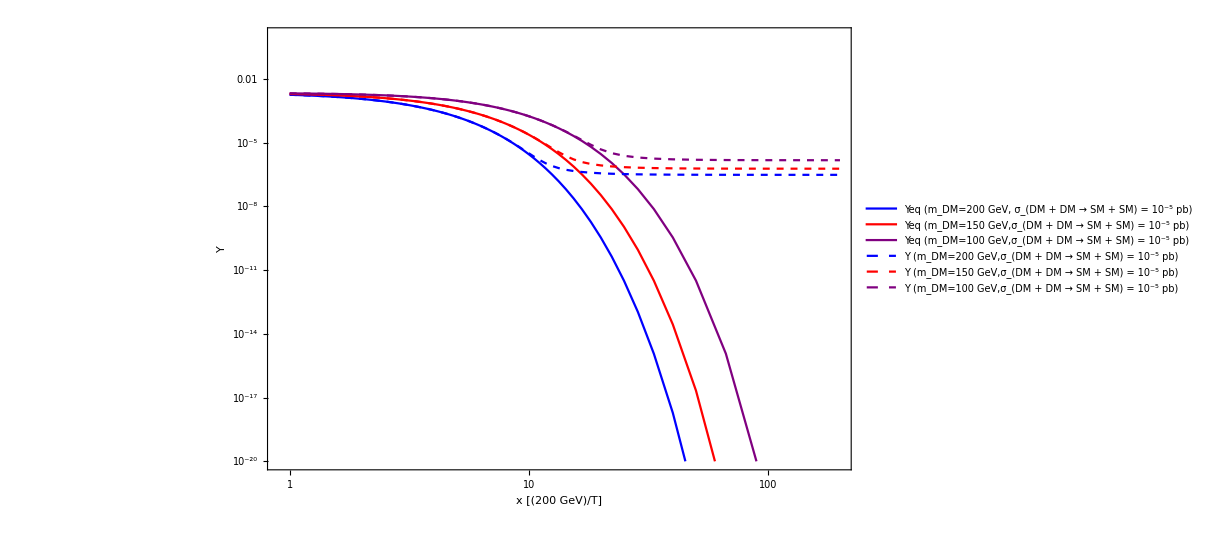

```mathematica
fileNames = {"C:\\Users\\AlexandrePoulin\\Documents\\relic\\oneDM\\out1_m.txt",
			"C:\\Users\\AlexandrePoulin\\Documents\\relic\\oneDM\\out2_m.txt",
			"C:\\Users\\AlexandrePoulin\\Documents\\relic\\oneDM\\out3_m.txt"};
files = Import[#,"Data"]&/@fileNames;

massScale= 200.0;
dmSpecies = 1;

plotDataeq = {};
plotData = {};

For[i=1, i ≤ Length[files],i++,
For[j=1, j≤ dmSpecies,j++,
AppendTo[plotDataeq,Table[{massScale/files[[i]][[a]][[1]],files[[i]][[a]][[2*j]]},{a,Length[files[[i]]]}]];
AppendTo[plotData,Table[{massScale/files[[i]][[a]][[1]],files[[i]][[a]][[2*j+1]]},{a,Length[files[[i]]]}]];
]
]


plot1=ListLogLogPlot[plotDataeq,PlotRange->{{0.9,200},{10^(-20),1}},Joined->True,PlotStyle->{Blue,Red,Purple},PlotLegends->{"Yeq (m_DM=200 GeV, σ_(DM + DM → SM + SM) = 10^-5 pb)","Yeq (m_DM=150 GeV,σ_(DM + DM → SM + SM) = 10^-5 pb)","Yeq (m_DM=100 GeV,σ_(DM + DM → SM + SM) = 10^-5 pb)"}];
plot2=ListLogLogPlot[plotData,PlotRange->{{0.9,200},{10^(-20),1}},Joined->True,PlotStyle->{{Dashed,Blue},{Dashed,Red},{Dashed,Purple}},PlotLegends->{"Y (m_DM=200 GeV,σ_(DM + DM → SM + SM) = 10^-5 pb)","Y (m_DM=150 GeV,σ_(DM + DM → SM + SM) = 10^-5 pb)","Y (m_DM=100 GeV,σ_(DM + DM → SM + SM) = 10^-5 pb)"}];
Show[{plot1,plot2},BaseStyle->{FontSize->40},Frame-> True,FrameLabel->{"x [(200 GeV)/T]","Y"},FrameStyle->Thick,FrameTicksStyle->Thick,ImageSize->{900,600}]
```